```mathematica
pUnrep :=1200;
Kd:=800;
n:=2;
tauR:=120;
tauP:=3600;
gr:=Log[2]/tauR;
gp:=Log[2]/tauP;
b:=10;
kp:=b*gr;
krmax:=pUnrep*gr*gp/kp;
```

```mathematica
kr[p_,n_,Kd_]:=krmax/(1+(p/Kd)^n);
Derivkr[p_,n_,Kd_]:=-(krmax n (p/Kd)^(-1+n))/(Kd (1+(p/Kd)^n)^2);
k0[pAve_,n_,Kd_]:=kr[pAve,n,Kd]-pAve*Derivkr[pAve,n,Kd];
k1[pAve_,n_,Kd_]:=-Derivkr[pAve,n,Kd];
pAve[n_,Kd_]:=({p,r}/.NSolve[0==kr[p,n,Kd,krmax]-gr*r&&0==kp*r-gp*p,{p,r},Reals])
which[n_,Kd_]:=Select[pAve[n,Kd],#[[1]]>0&][[1]][[1]]
pAveA[k0_,k1_]:=(1/(1+b*k1/gp))*(k0*b)/gp;
fano[k1_]:=((1-k1/gp)/(1+b*k1/gp))*b/(1+gp/gr)+1;
```

```mathematica
toplotN =Table[{which[n,Kd],fano[k1[which[n,Kd],n,Kd]]},{n,0,20,0.5}];
toplotKd=Table[{which[n,Kd],fano[k1[which[n,Kd],n,Kd]]},{Kd,0,5000,100}];
```

Power::infy: Infinite expression 1/0 encountered.

Part::partw: Part 1 of {} does not exist.

Power::infy: Infinite expression 1/0 encountered.

Part::partw: Part 1 of {} does not exist.

Power::infy: Infinite expression 1/0 encountered.

General::stop: Further output of Power :: infy will be suppressed during this calculation.

```mathematica
p2=ListPlot[{toplotN,toplotKd},Joined->True];
```

```mathematica
NN=Import["/home/gutiloluis/61Monograph/gillespie/n.dat"];
KD=Import["/home/gutiloluis/61Monograph/gillespie/Kd.dat"];
```

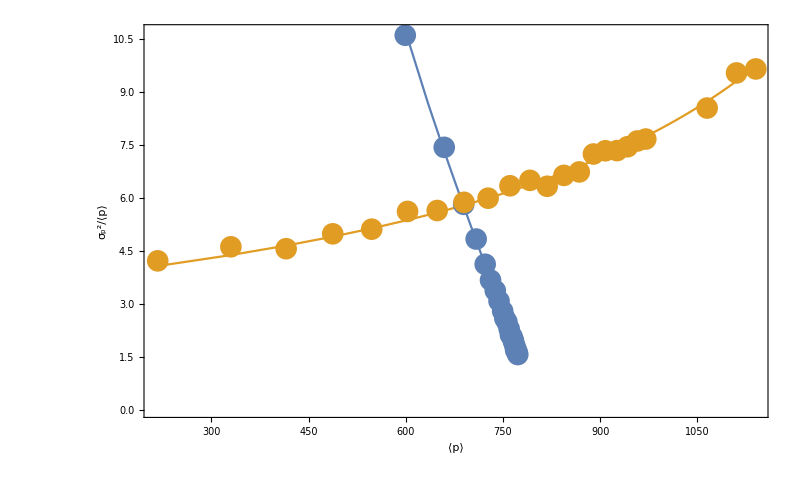

```mathematica
p3=ListPlot[{NN,KD},PlotRange->{0,12}];
Show[{p2,p3},ImageSize->800,Frame->True,FrameStyle->Black,FrameLabel->{Text[Style[ToExpression["\\langle p\\rangle",TeXForm,HoldForm],Large]],Text[Style[ToExpression["\\frac{\\sigma_p^2}{\\langle p\\rangle}",TeXForm,HoldForm],30]]},RotateLabel->False,LabelStyle->Directive[18,FontFamily->"Palatino Linotype",Black]]
```